```mathematica
(* Radiative Quenching, Chapter 3 *)

(* This one uses the Zygelman, Dalgrano ETF correction *)
(* Upper Limit for integration *)
limit = 10;

(* Reduced Mass *)
μ=1;
Subscript[m, p]=1836;
hbar= 1;  
c=137 ;(*SpeedOfLight*)
 
vSg1Data = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg1.mx"];
vSg2Data = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg2.mx"];

(* Load Potential curves for 1sg, 2sg states 
"R","p", "A","E","E+1/r"*)
(* 1sg state, potential curve *)
Subscript[v, a]=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,5]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, b]=Interpolation[Transpose[{vSg2Data[[All,1]],vSg2Data[[All,5]]}], InterpolationOrder->3];

deltaV[r_]:=Subscript[v, a][r]-Subscript[v, b][r];

(* calculate Transition dipole moment *)
(* Subscript[ψ, a](r)=f, Subscript[ψ, b](r)=g *)
solA[r_]:= Sort[Transpose[NDEigensystem[-1/(2μ)f''[x]+Subscript[v, a][r]f[x],f[x],{x,0.1,limit},All,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}] ]] [[1]][[2]];

solB[r_]:=Sort[Transpose[NDEigensystem[-1/(2μ)g''[x]+Subscript[v, b][r]g[x],g[x],{x,0.1,limit},All,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}] ]] [[1]][[2]];

(* radial transition dipole moment d(R)= <Subscript[ψ, a](R) R Subscript[ψ, b](R)> *)
(*d[r_]:=NIntegrate[(solA[r] /. x ->y)r (solB[r] /. x ->y), {y , .2, limit}]*)

fTemp[r_ ]:=solA[r] * r * solB[r];

d[r_]:=Map[NIntegrate[# , {x,.1, 10}] & ,fTemp[r]];

(* Calculate A(R)*)
a[r_]:=4/3(d[r])^2(deltaV[r])^3/c^3 ;
```

```mathematica
solNear=Sort[Transpose[NDEigensystem[-1/(2μ)ff''[x]+(Subscript[v, a][x]-I/2 a[x])ff[x],ff,{x,0.2, limit}, 10,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«19601»},{«1»}},{0.000133333+0. ⅈ,-0.0000333333+0. ⅈ,0.0000666667+0. ⅈ,-0.0000333333+0. ⅈ,0.000266667+0. ⅈ,«78392»,0.000533333+0. ⅈ,0.0000666667+0. ⅈ,0.0000666667+0. ⅈ,0.000533333+0. ⅈ}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
(* k = √(2 mE/ℏ)*)
kN =(√(2 Subscript[m, p] solNear[[1]][[1]]))/hbar;
kS = solNear[[1]][[1]];
fNear=solNear[[1]][[2]];
```

```mathematica
(* Now to calculate the phase shift we match the Subscript[f, R] in the region V = 0 with the solution in V = 0 , which is represented by the Bessel Functions. *)
(* We use logarithmic derivative *)

logBeta[x_] := fNear'[x]/fNear[x];
kN
Table[{i,logBeta[i]},{i,.5,5,.5}] //MatrixForm
```

19751.+19747.6 ⅈ

(0.5 | 133.965+249.413 ⅈ
1. | -1466.11+1258.89 ⅈ
1.5 | 474.958-676.005 ⅈ
2. | 5414.9+2083.93 ⅈ
2.5 | 338.272+260.331 ⅈ
3. | -563.403-997.893 ⅈ
3.5 | -1032.19+1269.22 ⅈ
4. | -397.076+678.593 ⅈ
4.5 | -293.77+153.217 ⅈ
5. | -41.3961+115.245 ⅈ)

```mathematica
(* For far away region *)
(* S wave *)

tanPhase1[k_,r_]:=(k r BesselJ'[0,k r]-logBeta[r]BesselJ[0,k r])/(k r BesselY'[0,k r]-logBeta[r]BesselY[0,k  r]);

tanPhase2[k_,r_]:=(k r Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k r Sin[k  r]);

tanPhase3[k_,r_]:=(k Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k  Sin[k  r]);
```

```mathematica
Table[{r,tanPhase1[kS,r]},{r,5,20,1}]
Table[{r,tanPhase2[kS,r]},{r,5,20,1}]
Table[{r,tanPhase3[kS,r]},{r,5,20,1}]
```

```mathematica
tanPhase[k_,r_] := (k N[BesselJ[0, k r ]]-Abs[Subscript[logf, R][r]] N[BesselY[0, k r]])/(Abs[Subscript[logf, R][r]] N[BesselJ[0, k r ]]+k N[BesselY[0, k r]]);
kk = Abs[solF[[1]][[1]]];
```

```mathematica
tanPhase[1,5] 
tanPhase[kk,8] 
tanPhase[kk,9] 
tanPhase[kk,10] 
tanPhase[kk,20] 
tanPhase[kk,30] 
tanPhase[kk,40] 
tanPhase[kk,50]
```

(-0.177597+0.308518 Abs[logf_R[5]])/(-0.308518-0.177597 Abs[logf_R[5]])

(0.0331852-0.520705 Abs[logf_R[8]])/(0.141857+0.121811 Abs[logf_R[8]])

(-0.0065902-0.504576 Abs[logf_R[9]])/(0.137463-0.0241902 Abs[logf_R[9]])

(-0.0417096-0.454856 Abs[logf_R[10]])/(0.123918-0.153101 Abs[logf_R[10]])

(-0.00665868+0.340257 Abs[logf_R[20]])/(-0.0926971-0.0244416 Abs[logf_R[20]])

(0.0351855-0.247124 Abs[logf_R[30]])/(0.0673247+0.129153 Abs[logf_R[30]])

(-0.0513519+0.151094 Abs[logf_R[40]])/(-0.0411629-0.188494 Abs[logf_R[40]])

(0.0568866-0.0557067 Abs[logf_R[50]])/(0.0151763+0.20881 Abs[logf_R[50]])

```mathematica
0.6859018741706624
ArcTan[0.68]
```

0.685902

0.597177

```mathematica
(* Phase shift *)
δ[k_]:=ArcTan[tanPhase[k,10]];
```

0.601201

-0.263234

0.272131

1.38178

0.408682

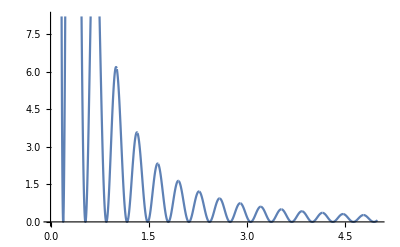

```mathematica
σ[k_]:=2 π/k^2 Sin[δ[k]]^2;
Plot[σ[k],{k, 0,5}]
```